```mathematica
ClearAll["Global`*"];

G = 6.67 * 10^-11;

Mz = 5.96 * 10^24;

Fg = G * (m*Mz)/R^2;

Fod = (m * v^2)/R;

r1 = Solve[Fg == Fod, v]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{v→-(1.99382×10^7)/(√R)},{v→(1.99382×10^7)/(√R)}}

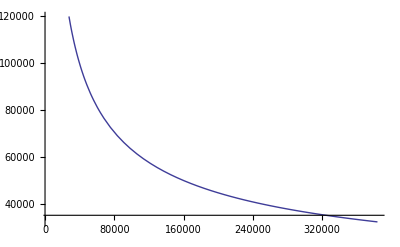

```mathematica
v[R_] = v /. r1[[2,1]];

Plot[v[R], {R, 6370, 3.84 * 10^5}]
```

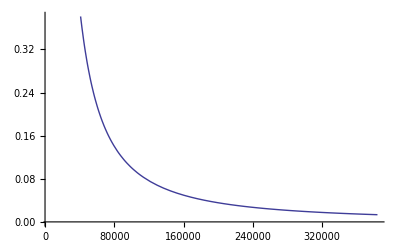

```mathematica
pi = 3.14;

f = v/( 2*pi * R);

Plot[f /. r1[[2,1]], {R, 6370, 3.84 * 10^5}]
```